```mathematica
Clear[x,y]
DSolve[{y'[x]==x+y[x],y[0]==2},y[x],x]
(*Common Mistakes
Capital S,
Brackets,
Clear[x,y]*)
```

{{y[x]→-1+3 ⅇ^x-x}}

```mathematica
Clear[x,y]
DSolve[{y''[x]+y[x]==0,y[0]==0,y[π/2]==1},y[x],x]
(*Common Mistakes
Capital S,
Brackets,
Clear[x,y]*)
```

{{y[x]→Sin[x]}}

```mathematica
Clear[x,y,f,s]
s= DSolve[{y''[x]+y[x]==1,y[0]==0,y[1]==0},y[x],x]
(*Common Mistakes
Capital S,
Brackets,
Clear[x,y,f,s]*)
```

{{y[x]→1-Cos[x]+Cot[1] Sin[x]-Csc[1] Sin[x]}}

```mathematica
f[x_]=s[[1,1,2]]
(*Common Mistakes
f[x_]:= means no output,
Brackets double [[]],
use _ *)
```

1-Cos[x]+Cot[1] Sin[x]-Csc[1] Sin[x]

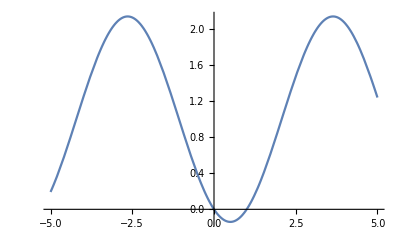

```mathematica
Plot[f[x],{x,-5,5},Axes->True]
(*Common Mistakes
Capital P,
Brackets,
no use of _ *)
```